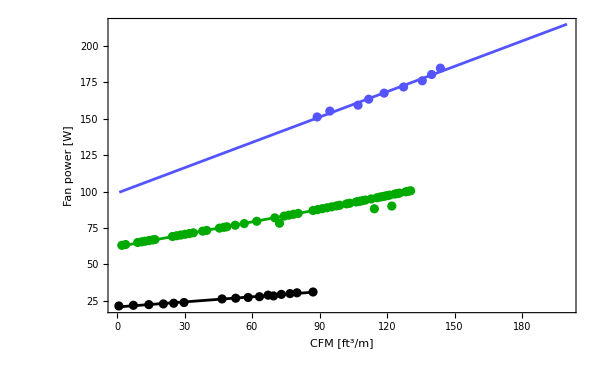

```mathematica
(*Fans*)
nfans=4;
QCFM=nfans{0.21,1.82,3.54,5.15,6.30,7.45,11.67,13.19,14.57,15.83,17.39,16.79,18.26,19.22,20.00,21.78};
Ptot=nfans{5.35698687,5.472198511,5.588634921,5.7062961,5.82518205,5.945292769,6.564217911,6.691677249,6.820361356,6.950270233,7.08140388,7.213762297,7.347345483,7.482153439,7.618186165,7.755443661};
QCFMP=Table[{QCFM[[i]],Ptot[[i]]},{i,1,Length[QCFM]}];
QCFM2=nfans{22.24,23.65,26.78,27.97,29.68,31.84,33.92,34.96,35.93};
Ptot2=nfans{37.82,38.82375,39.84,40.86875,41.91,42.96375,44.03,45.10875,46.2};
QCFMP2=Table[{QCFM2[[i]],Ptot2[[i]]},{i,1,Length[QCFM2]}];
SetDirectory[NotebookDirectory[]];
QCFM3=nfans Flatten[Import["text.dat"]];
Ptot3=nfans Flatten[Import["text2.dat"]];
QCFMP3=Table[{QCFM3[[i]],Ptot3[[i]]},{i,1,Length[QCFM3]}];
{a1,b1}={a,b}/.FindFit[QCFMP,a+b x,{a,b},x];
{a2,b2}={a,b}/.FindFit[QCFMP2,a+b x,{a,b},x];
{a3,b3}={a,b}/.FindFit[QCFMP3,a+b x,{a,b},x];
Show[Plot[a1+b1 x,{x,0,QCFM[[-1]]},PlotRange->{{0,200.},All},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->600,FrameLabel->{"CFM [ft^3/m]","Fan power [W]"},FrameStyle->Directive[Black,18]],Plot[a2+b2 x,{x,1,200},PlotRange->All,PlotStyle->Lighter[Blue]],Plot[a3+b3 x,{x,QCFM3[[1]],Max[QCFM3]},PlotRange->All,PlotStyle->Darker[Green]],
ListPlot[{QCFMP,QCFMP2,QCFMP3},PlotStyle->{Black,Lighter[Blue],Darker[Green]}]]
fCFMtoPower[CFM_]:=If[CFM<QCFMP[[-1,1]],a1+b1 CFM,If[CFM<Max[QCFMP3[[All,1]]] ,a3+b3 CFM,a2+b2 CFM]]
(*fCFMtoPower[CFM_]:=a2+b2 CFM*)
```

```mathematica
a1+b1 200
```

44.0431

```mathematica
3.54 10^6 ((2 10^-3)^2-(200 10^-6)^2)
6.25 10^7(200 10^-6)^2
```

14.0184

2.5

```mathematica
{1,2,3}*3.54 10^6
{1,2,3}*6.25 10^7
```

```mathematica
{3.54*^6,7.08*^6,1.062*^7}
```

```mathematica
{6.25*^7,1.25*^8,1.875*^8}
```

```mathematica
Puni={0.1,0.2,0.5,1,2,5,10}*3.54 10^6 (2 10^-3)^2 16
Puni2={0.1,0.2,0.5,1,2,5,10}*3.54 10^6 ((2 10^-3)^2-(200 10^-6)^2)16
Phs={0.1,0.2,0.5,1,2,5,10}*6.25 10^7(200 10^-6)^2 16
Ptot=Puni2+Phs
```

{22.656,45.312,113.28,226.56,453.12,1132.8,2265.6}

{22.4294,44.8589,112.147,224.294,448.589,1121.47,2242.94}

{4.,8.,20.,40.,80.,200.,400.}

{26.4294,52.8589,132.147,264.294,528.589,1321.47,2642.94}

```mathematica
Table[{Puni[[i]],0},{i,1,Length[Puni]}]
Table[{Ptot[[i]],0},{i,1,Length[Puni]}]
```

{{22.656,0},{45.312,0},{113.28,0},{226.56,0},{453.12,0},{1132.8,0},{2265.6,0}}

{{26.4294,0},{52.8589,0},{132.147,0},{264.294,0},{528.589,0},{1321.47,0},{2642.94,0}}

```mathematica
26.25+(x-22.656)/(45.312-22.656)(32.62-26.25)
```

26.25+0.281162 (-22.656+x)

```mathematica
(CFM87[[2,2]]-CFM87[[1,2]])/(CFM87[[2,1]]-CFM87[[1,1]])
(CFM200[[2,2]]-CFM200[[1,2]])/(CFM200[[2,1]]-CFM200[[1,1]])
(CFM87hs[[2,2]]-CFM87hs[[1,2]])/(CFM87hs[[2,1]]-CFM87hs[[1,1]])
(CFM200hs[[2,2]]-CFM200hs[[1,2]])/(CFM200hs[[2,1]]-CFM200hs[[1,1]])
```

0.281162

0.237465

0.427174

0.384041

```mathematica
CFM87={{22.656,26.25},{45.312,32.62},{113.28,51.65},{226.56,83.26},{453.12,146.3},{1132.8,335.4},{2265.6,650.8}};
CFM200={{22.656,25.25},{45.312,30.63},{113.28,46.7},{226.56,73.33},{453.12,126.3},{1132.8,284.8},{2265.6,548.3}};
CFM87hs={{26.4294,31.18},{52.8589,42.47},{132.147,76.27},{264.294,132.5},{528.589,244.7},{1321.47,581.4},{2642.94,1143}};
CFM200hs={{26.4294,30.01},{52.8589,40.16},{132.147,70.49},{264.294,120.9},{528.589,221.3},{1321.47,522.1},{2642.94,1023}};
CFM87=Table[{CFM87hs[[i,1]],CFM87[[i,2]]},{i,1,Length[CFM87]}];CFM200=Table[{CFM200hs[[i,1]],CFM200[[i,2]]},{i,1,Length[CFM200]}];
```

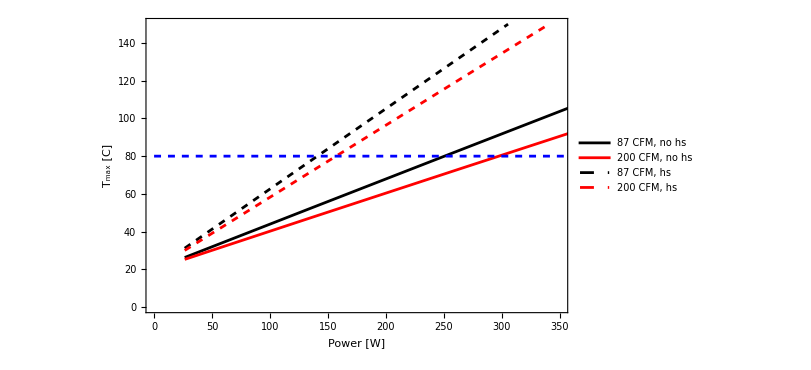

```mathematica
Show[ListPlot[{CFM87,CFM200,CFM87hs,CFM200hs},PlotRange->{{0,350},{0,150}},PlotStyle->{{Black},{Red},{Black,Dashed},{Red,Dashed}},Frame->True,FrameLabel->{"Power [W]","T_max [C]"},ImageSize->600,Joined->True,Mesh->None,PlotLegends->Placed[{"87 CFM, no hs","200 CFM, no hs","87 CFM, hs","200 CFM, hs"},Scaled[{0.2,0.8}]]],Plot[80,{x,0,1000},PlotStyle->{Blue,Dashed}]]
```

```mathematica
(140+31)/31.
(157+215)/215.
(250+125)/125.
```

5.51613

1.73023

3.

```mathematica
CFM87total=Table[{CFM87hs[[i,1]],Phs[[i]]/0.2 0.5+31},{i,1,Length[CFM87]}];
CFM200total=Table[{CFM200hs[[i,1]],Phs[[i]]/0.2 0.5+215},{i,1,Length[CFM200]}];
```

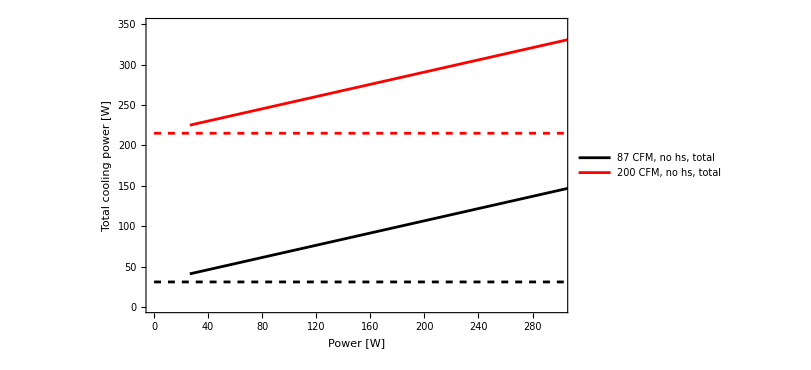

```mathematica
Show[ListPlot[{CFM87total,CFM200total},PlotRange->{{0,300},{0,350}},PlotStyle->{{Black},{Red},{Black,Dashed},{Red,Dashed}},Frame->True,FrameLabel->{"Power [W]","Total cooling power [W]"},ImageSize->600,Joined->True,Mesh->None,PlotLegends->Placed[{"87 CFM, no hs, total","200 CFM, no hs, total"},Scaled[{0.2,0.8}]]],Plot[{31,215},{x,0,400},PlotStyle->{{Black,Dashed},{Red,Dashed}}]]
```

```mathematica
Injected power 140 to 250 W
```

```mathematica
Total cooling power 31 to 125 W
```

```mathematica
Ptot
```

{26.4294,52.8589,132.147,264.294,528.589,1321.47,2642.94}

```mathematica
Phs/0.2 0.5
```

{10.,20.,50.,100.,200.,500.,1000.}

```mathematica
F[NOHS_,HS_,TOTLasPower_,LasPower_]:=Table[{NOHS[[i,1]],HS[[i,2]]+LasPower/TOTLasPower(NOHS[[i,2]]-HS[[i,2]])},{i,1,Length[NOHS]}]
```

```mathematica
Manipulate[Show[ListPlot[{T1nh,T1h,F[T1nh,T1h,100.,LasPower]},Frame->True,FrameLabel->{"CFM [ft^3/m]","T_hs(C)"},Joined->True,Mesh->All,ImageSize->600],Plot[Tfinal,{x,0,200},PlotStyle->{Black,Dashed}]],{LasPower,0,100},{{Tfinal,120},50,300}]
```

```mathematica
fCFM[CFM_,NOHS_,HS_,TOTLasPower_,LasPower_]:=Interpolation[F[NOHS,HS,TOTLasPower,LasPower],InterpolationOrder->1][CFM]
```